```mathematica
Exit
```

```mathematica
rotL[data_]:=RotateLeft[data, Floor@Dimensions[data][[#]]/2&/@Range[Length@Dimensions[data]]];
(* corner at orign to center at origin *)
rotR[data_]:=RotateRight[data, Floor@Dimensions[data][[#]]/2&/@Range[Length@Dimensions[data]]];
(* {x,y} means {x,y}/λ, {kx,ky} means {kx,ky}/k *)
FFT[f_] :=rotR[Fourier[f, FourierParameters->{1, -1}]];
iFFT[f_]:=InverseFourier[rotL[f], FourierParameters->{1, -1}];

centerRange[n_,d_]:=Table[(i-n/2-.5)*d,{i,n}];

(*plot[plotFunction_,func_, args_]:=Map[func/*plotFunction, args, {2}]//GraphicsGrid//Rasterize;*)
Options[plot]={plotFunction->ArrayPlot, cropRatio->1, rasterize->True};
plot[func_, args_, OptionsPattern[]]:=
Module[{},
	Map[func/*(ArrayPad[#,-Floor[(1-OptionValue[cropRatio])/2*Dimensions@#]]&)/*OptionValue[plotFunction], 
	args, {2}]//GraphicsGrid
	]
```

```mathematica
T={{({{-1, 1, 1, 1}, {1, -1, 1, 1}, {1, 1, -1, 1}, {1, 1, 1, -1}}),f },{({{-1, -1, -1, -1}, {-1, -ⅈ, 1, ⅈ}, {-1, 1, -1, 1}, {-1, ⅈ, 1, -ⅈ}}),2f}};
testFarField=ArrayReshape[IdentityMatrix[4],{2,2,2,2}];
testGrover={{({{-1, 1}, {1, 1}}),({{1, -1}, {1, 1}}),({{1, 1}, {-1, 1}}),({{1, 1}, {1, -1}})}};
testQFT={{({{1, 1}, {1, 1}}),({{1, -ⅈ}, {-1, ⅈ}}),({{1, -1}, {1, -1}}),({{1, ⅈ}, {-1, -ⅈ}})}};
```

```mathematica
(* 20um lens*)
p=0.31 2;
size=32p;
λ=0.810;
θx=10Degree;
θy=10Degree;
f=150;
padRatio=5;
```

```mathematica
k0=2π/λ;
{nx,ny}={Floor[size/p],Floor[size/p]};
{lx,ly}={nx*p,ny*p};
{dx,dy}={p,p};
{dkx, dky}={(2π)/(p*nx),(2π)/(p*ny)};
{padx,pady}= {3(padRatio-1)/2 nx,3(padRatio-1)/2 ny};
k = k0*Sin/@({{{-θx, -θy}, {θx, -θy}}, {{-θx, θy}, {θx, θy}}})//N;
r0 = -p/2*({{{-nx, -ny}, {nx, -ny}}, {{-nx, ny}, {nx, ny}}})//N;
{kx,ky}={Flatten@Part[k, ;;,;;,1],Flatten@Part[k, ;;,;;,2]};
{x0,y0}={Flatten@Part[r0, ;;,;;,1],Flatten@Part[r0, ;;,;;,2]};
{fx,fy}={(f*kx)/Sqrt[k0^2-kx^2],(f*ky)/Sqrt[k0^2-ky^2]};
{x,y}={centerRange[nx,dx],centerRange[ny,dy]};
Echo[{nx p,ny p},"Sample size in um: "];
Echo[{nx,ny},"Sample size in pixel: "];
```

Sample size in um:   {19.84,19.84}

Sample size in pixel:   {32,32}

FOCUSING LENS

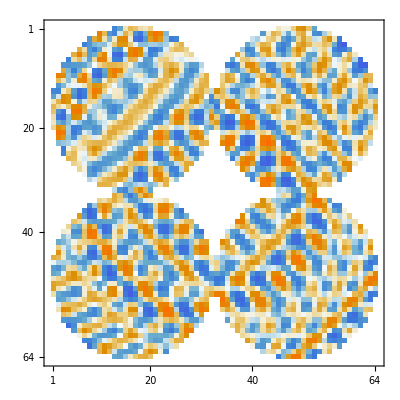

```mathematica
(*f2x[f_]:=(f*kx)/Sqrt[k0^2-kx^2];
f2y[f_]:=(f*ky)/Sqrt[k0^2-ky^2];*)
ellipticalMask:=Map[If[#<(lx ly)/4,1,0]&,Outer[Plus,y^2,x^2],{2}];
globalEllipticalMask := KroneckerProduct[({{1, 1}, {1, 1}}), ellipticalMask];
eGlobalLens[arg_]:= ArrayFlatten[Map[eLocalLens,arg,{2}]];
eGlobalInput[arg_]:=ArrayFlatten[Map[#*ConstantArray[1,{ny,nx}]&,arg,{2}]];
H[A_,z_,{dx_,dy_}] := Module[{nx, ny, kx, ky},
	{nx, ny}=Dimensions[A][[#]]&/@{2,1};
	{kx,ky}=centerRange@@#&/@{{nx, (2π)/(dx nx)},{ny,(2π)/(dy ny)}};
	Exp[I *z*Sqrt[k0^2 - Outer[Plus,ky^2,kx^2]]]
]; 
forwardPropagate[A_,z_,{dx_, dy_}]:=iFFT[FFT[A] *H[A,z,{dx, dy}]];

(*Method 1: shift the center of the lens by fx,fy;
	but the lens interference might not be perfect *)
eLocalLens[i_] := 
Sum[
Module[{T2=T[[k]][[1]],f=T[[k]][[2]]},
Sum[T2[[j]][[i]]* Exp[-ⅈ*k0*(√(Outer[Plus,(y-y0[[i]]-fy[[j]])^2,(x-x0[[i]]-fx[[j]])^2]+f^2)-f)]
*ellipticalMask,{j,4}]
],{k,2}];

(* Method 2: focus at the center and deflect the beam, but the focusing plane is not parallel with the optical axis. *)
eLocalLens[i_] := 
Sum[
Module[{T2=T[[k]][[1]],f=T[[k]][[2]]},
Sum[T2[[j]][[i]]* Exp[-ⅈ k0√(Outer[Plus,(y-y0[[i]])^2,(x-x0[[i]])^2]+(f^2+fy[[j]]^2+fx[[j]]^2))
+ⅈ Outer[Plus,ky[[j]](y-y0[[i]]),kx[[j]](x-x0[[i]])]]
*ellipticalMask,{j,4}]
],{k,2}];

farField[arg_,z_]:=forwardPropagate[ArrayPad[eGlobalInput[arg]*meta,{{pady}, {padx}}],z, {p, p}]//Abs[#]^2&;
meta=eGlobalLens[({{1, 2}, {3, 4}})];
meta//MatrixPlot
```

```mathematica
SetOptions[plot, cropRatio->0.7];

Echo["Test Grover"];
plot[farField[#,f]&,testGrover]//Rasterize

Echo["Test QFT"];
plot[farField[#,2f]&,testQFT]//Rasterize
```

Test Grover

-Graphics-

Test QFT

-Graphics-